```mathematica
fstart=0;
fend=10;
velocity=5;
```

```mathematica
Integrate[Exp[(-(x-f)^2)/2]/1,{f,0,1}]
```

√(π/2) (Erf[(1-x)/(√2)]+Erf[x/(√2)])

```mathematica
ρf[x_,t_]:=Module[{f0,f1,δleft,δright,middle},
f0=(fend-fstart)/1(t-1/velocity);
f1=(fend-fstart)/1(t);
δleft[xp_]=DiracDelta[xp-fstart]*Min[Max[0,(fstart-f0)/(f1-f0)],1];
δright[xp_]=DiracDelta[xp-fend]*Min[Max[0,(f1-fend)/(f1-f0)],1];
middle[xp_]=UnitStep[xp-f0,f1-xp]/(f1-f0)*UnitStep[xp-fstart]*UnitStep[fend-xp];
δleft[x]+δright[x]+middle[x]
]
```

```mathematica
Convolve[Exp[-x^2/2],ρf[x,t],x,y]
```

ⅇ^(-y^2/2) Min[1,Max[0,-(10 (-1/5+t))/(-10 (-1/5+t)+10 t)]]+ⅇ^(-1/2 (-10+y)^2) Min[1,Max[0,(-10+10 t)/(-10 (-1/5+t)+10 t)]]+1/(-10 (-1/5+t)+10 t)√(π/2) (DiscreteDelta[-t] (Erf[(10 t-y)/(√2)]+Erf[y/(√2)])-(Erf[(10 t-y)/(√2)]+Erf[(2-10 t+y)/(√2)]) (UnitStep[-1+t]-UnitStep[t])+(Erf[y/(√2)]-Erf[(2-10 t+y)/(√2)]) UnitStep[2-10 t,t]+(-Erf[(-10+y)/(√2)]+Erf[(2-10 t+y)/(√2)]) UnitStep[12-10 t,-1+t])

```mathematica
Table[Evaluate[Convolve[Exp[-x^2/2],ρf[x,t],x,y]/.fstart->0/.fend->10/.velocity->5/.t->ii],{ii,0,1,0.5}]
```

{ⅇ^(-y^2/2)+0.626657 (2 Erf[(0.-y)/(√2)]+2 Erf[y/(√2)]),0.626657 (Erf[(5.-y)/(√2)]+Erf[(-3.+y)/(√2)]),0.+0.626657 (-Erf[(-10+y)/(√2)]+Erf[(-8.+y)/(√2)])}

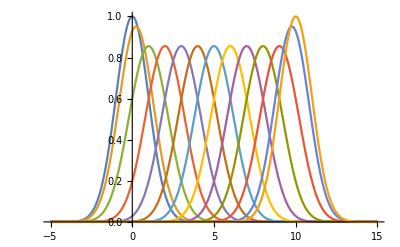

```mathematica
Plot[Evaluate@Table[Evaluate[Convolve[Exp[-x^2/2],ρf[x,t],x,y]/.fstart->0/.fend->10/.velocity->5/.t->ii],{ii,0,1.2,0.1}],{y,-5,15},PlotRange->All]
```

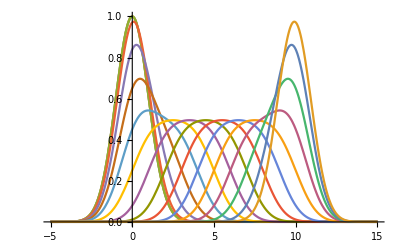

```mathematica
Plot[Evaluate@Table[Evaluate[Convolve[Exp[-x^2/2],ρf[x,t],x,y]/.fstart->0/.fend->10/.velocity->2/.t->ii],{ii,-0.2,1.4,0.1}],{y,-5,15},PlotRange->All]
```

```mathematica
ρf[x_,t_]:=Module[{f0,f1,δleft,δright,middle},
f0=(fend-fstart)/1(t-1/velocity);
f1=(fend-fstart)/1(t);
δleft[xp_]=DiracDelta[xp-fstart]*Min[Max[0,(fstart-f0)/(f1-f0)],1];
δright[xp_]=DiracDelta[xp-fend]*Min[Max[0,(f1-fend)/(f1-f0)],1];
middle[xp_]=UnitStep[xp-f0,f1-xp]/(f1-f0)*UnitStep[xp-fstart]*UnitStep[fend-xp];
δleft[x]+δright[x]+middle[x]
]
```

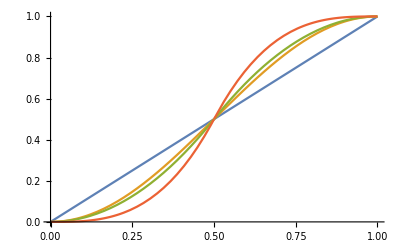

```mathematica
Plot[{x,Sin[x*Pi/2]^2,If[x<0.5,2 x^2,1-2(1-x)^2],If[x<0.5,4 x^3,1-4(1-x)^3]},{x,0,1}]
```

```mathematica
D[Sin[x*Pi/2]^2,x]
```

π Cos[(π x)/2] Sin[(π x)/2]

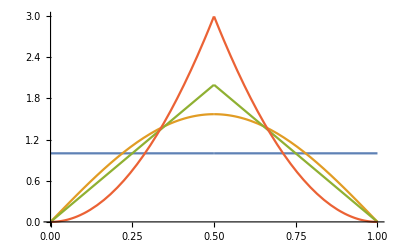

```mathematica
Plot[{Evaluate@D[x,x],Evaluate@D[Sin[x*Pi/2]^2,{x}],Evaluate@D[If[x<0.5,2 x^2,1-2(1-x)^2],x],Evaluate@D[If[x<0.5,4 x^3,1-4(1-x)^3],x]},{x,0,1}]
```

```mathematica
|
```

```mathematica
D[x^3,x]
```

```mathematica
1/D[x,x]
```

1

```mathematica
1/D[Sin[x]^2,x]
```

1/2 Csc[x] Sec[x]